## Nondimensionalizing: rescaling variables

```mathematica
f[S_] = r S (1-S/K);
```

```mathematica
vals1 = {r->2, K->7};
sol1 = NDSolve[{S'[t]==(f[S[t]]/.vals1),S[0]==(0.1*K/.vals1)},S,{t,0,10}]
vals2 = {r->4, K->2};
sol2 = NDSolve[{S'[t]==(f[S[t]]/.vals2),S[0]==(0.1*K/.vals2)},S,{t,0,10}]
```

```mathematica
{{S->InterpolatingFunction[…]}}
```

{{S→InterpolatingFunction[…]}}

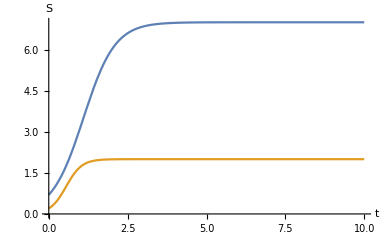

```mathematica
Plot[{S[t]/.sol1, S[t]/.sol2},{t,0,10},AxesLabel->{"t","S"},LabelStyle->Medium]
```

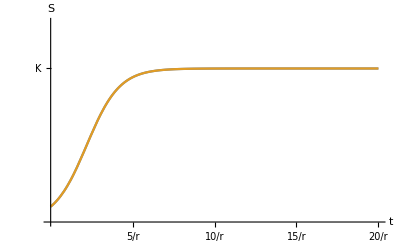

```mathematica
Plot[{(S[τ/r]/K)/.sol1/.vals1, (S[τ/r]/K)/.sol2/.vals2},{τ,0,20},AxesLabel->{"t","S"},PlotRange->{{0,20},{0,1.3}},LabelStyle->Medium,Ticks->{{{5,"5/r"},{10,"10/r"},{15,"15/r"},{20,"20/r"}},{{1,"K"}}}]
```

## Nondimensionalizing: bringing quantities to the same order of magnitude

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{V→0.,T→0.,Inf→0.},{V→0.,T→7.×10^7,Inf→0.},{V→32419.,T→1.09091×10^7,Inf→2.35774×10^6}}

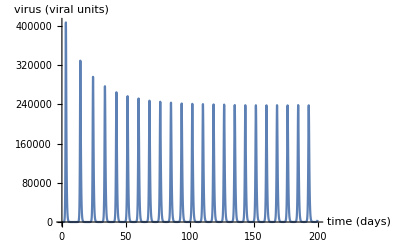

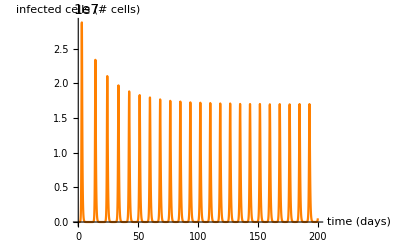

```mathematica
eqtns = {p Inf - c V - β V T, g T (1-(T+Inf)/Ct) - β1 V T, β1 V T - δ Inf}/.{p->0.35,c->20,β->5*10^-7,g->0.8,Ct->7*10^7,β1->2*10^-5,δ->3};
Solve[eqtns==0,{V, T, Inf}]
sol=NDSolve[{{V'[t],T'[t],Inf'[t]}==((eqtns)/.Inf->Inf[t]/.V->V[t]/.T->T[t]),V[0]==1, T[0]==7*10^7,Inf[0]==0},{V[t],T[t],Inf[t]}, {t,0,1000}];
Plot[V[t]/.sol,{t,0,200},PlotRange->Full,AxesLabel->{"time (days)", "virus (viral units)"},LabelStyle->{Medium,Black}]
Plot[Inf[t]/.sol,{t,0,200},PlotRange->Full,AxesLabel->{"time (days)", "infected cells (# cells)"},LabelStyle->{Medium,Black},PlotStyle->Orange]
```

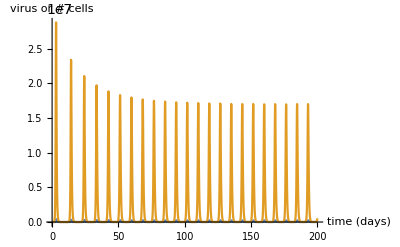

```mathematica
Plot[{V[t]/.sol,Inf[t]/.sol},{t,0,200},PlotRange->Full,AxesLabel->{"time (days)", "virus  or # cells"},LabelStyle->{Medium,Black}]
```

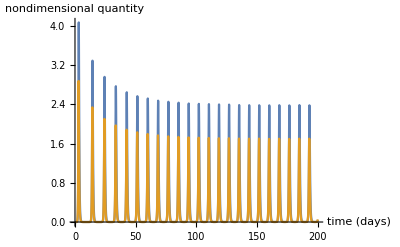

```mathematica
Plot[{V[t]/10^5/.sol,Inf[t]/10^7/.sol},{t,0,200},PlotRange->Full,AxesLabel->{"time (days)", "nondimensional quantity"},LabelStyle->{Medium,Black}]
```